## Calculate ED50 for logistic

```mathematica
Solve[0.5==1/(1+Exp[-(a + b Log[ϕ / d])]),d,Reals]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{d→(2.71828^(-1. a))^(-1./b) ϕ}}

## Plotting logistic

```mathematica
Manipulate[LogLinearPlot[1/(1+Exp[-(a + b Log[ϕ/d])]),{d,1,300},PlotRange->{Automatic,{0,1}}],{{a,2.0},0.2,10},{{b,1.5},0.2,10},{{ϕ,25},1,400}]
```

## Dose response

```mathematica
yticks=Table[{y,StringJoin[ToString[IntegerPart[100 y]],"%"]},{y,0,1,0.2}];
```

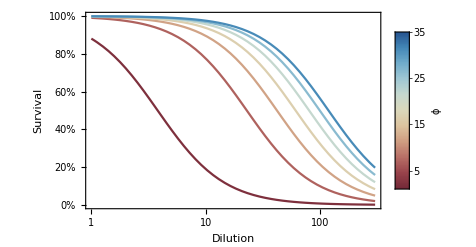

```mathematica
g1=Legended[Show[Table[LogLinearPlot[1/(1+Exp[-(a + b Log[ϕ/d])])/.{a->2,b->1.5},{d,1,300},PlotRange->{Automatic,{0,1}},PlotStyle->ColorData["RedBlueTones"][ϕ/35],Frame->{True,True,False,False},FrameLabel->{"Dilution","Survival"},LabelStyle->{Black,FontSize->16},FrameTicks->{Automatic,yticks}],{ϕ, 1,35,5}],ImageSize->400],BarLegend[{"RedBlueTones",{1,35}},LegendLabel->"ϕ",LabelStyle->Directive[Black,FontSize->16]]]
```

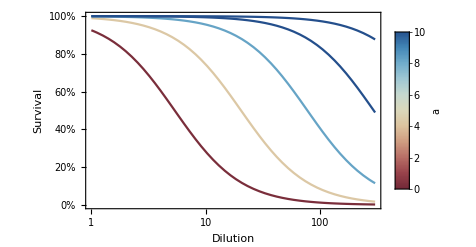

```mathematica
g2=Legended[Show[Table[LogLinearPlot[1/(1+Exp[-(a + b Log[ϕ/d])])/.{ϕ->5,b->1.5},{d,1,300},PlotRange->{Automatic,{0,1}},PlotStyle->ColorData["RedBlueTones"][a/5],Frame->{True,True,False,False},FrameLabel->{"Dilution","Survival"},LabelStyle->{Black,FontSize->16},FrameTicks->{Automatic,yticks}],{a,0.1,10,2}],ImageSize->400],BarLegend[{"RedBlueTones",{0,10}},LegendLabel->"a",LabelStyle->Directive[Black,FontSize->16]]]
```

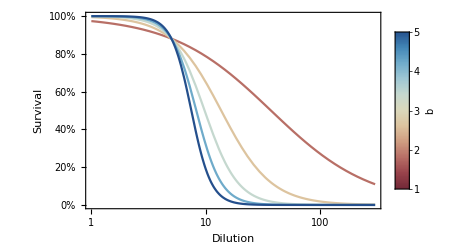

```mathematica
g3=Legended[Show[Table[LogLinearPlot[1/(1+Exp[-(a + b Log[ϕ/d])])/.{a->2,ϕ->5},{d,1,300},PlotRange->{Automatic,{0,1}},PlotStyle->ColorData["RedBlueTones"][b/5],Frame->{True,True,False,False},FrameLabel->{"Dilution","Survival"},LabelStyle->{Black,FontSize->16},FrameTicks->{Automatic,yticks}],{b,1,5,1}],ImageSize->400],BarLegend[{"RedBlueTones",{1,5}},LegendLabel->"b",LabelStyle->Directive[Black,FontSize->16]]]
```

```mathematica
g=Grid[{{g1},{g2},{g3}}]
```

-Graphics-
-Graphics-
-Graphics-

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Export["../../figures/dose_response_explainer.pdf",g]
```

../../figures/dose_response_explainer.pdf